```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\critical_region\LPA\fixpoint_initialcondition_v2\potential

## mub0

```mathematica
lam0=Flatten[Import["./mub0/buffer/lam0.dat"]]*197.33^4;
lam1=Flatten[Import["./mub0/buffer/lam1.dat"]]*197.33^2;
lam2=Flatten[Import["./mub0/buffer/lam2.dat"]]*197.33^0;
lam3=Flatten[Import["./mub0/buffer/lam3.dat"]]*197.33^-2;
lam4=Flatten[Import["./mub0/buffer/lam4.dat"]]*197.33^-4;
lam5=Flatten[Import["./mub0/buffer/lam5.dat"]]*197.33^-6;
V[ρ_]:=(*lam0+*)lam1 ρ+lam2/2. ρ^2+lam3/6. ρ^3+lam4/24. ρ^4+lam5/120. ρ^5;
```

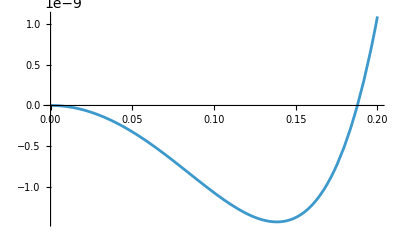

```mathematica
Plot[V[sigma^2/2]-V[0],{sigma,0,0.2}(*,ScalingFunctions->{Automatic,"Log"}*),PlotRange->All]
```

## mub750

```mathematica
lam0mub750=Flatten[Import["./mub750/buffer/lam0.dat"]]*197.33^4;
lam1mub750=Flatten[Import["./mub750/buffer/lam1.dat"]]*197.33^2;
lam2mub750=Flatten[Import["./mub750/buffer/lam2.dat"]]*197.33^0;
lam3mub750=Flatten[Import["./mub750/buffer/lam3.dat"]]*197.33^-2;
lam4mub750=Flatten[Import["./mub750/buffer/lam4.dat"]]*197.33^-4;
lam5mub750=Flatten[Import["./mub750/buffer/lam5.dat"]]*197.33^-6;
Vmub750[ρ_]:=(*lam0mub750+*)lam1mub750 ρ+lam2mub750/2. ρ^2+lam3mub750/6. ρ^3+lam4mub750/24. ρ^4+lam5mub750/120. ρ^5;
```

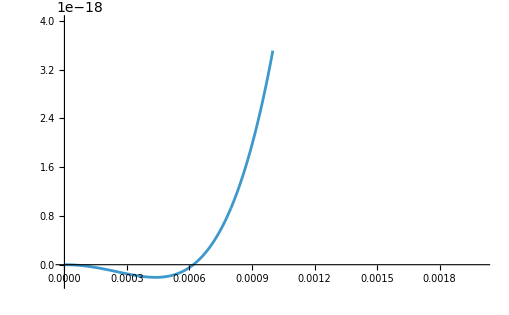

```mathematica
Plot[Vmub750[sigma^2/2]-Vmub750[0],{sigma,0,0.001}(*,ScalingFunctions->{Automatic,"Log"}*),PlotRange->{{0,0.002},{-3 10^-19,40 10^-19}}(*,Mesh->All*),PlotPoints->10000,MaxRecursion->10,WorkingPrecision->100,AccuracyGoal->100,PrecisionGoal->100]
```

## mub706p4

```mathematica
lam0mub750=Flatten[Import["./mub706p4/buffer/lam0.dat"]]*197.33^4;
lam1mub750=Flatten[Import["./mub706p4/buffer/lam1.dat"]]*197.33^2;
lam2mub750=Flatten[Import["./mub706p4/buffer/lam2.dat"]]*197.33^0;
lam3mub750=Flatten[Import["./mub706p4/buffer/lam3.dat"]]*197.33^-2;
lam4mub750=Flatten[Import["./mub706p4/buffer/lam4.dat"]]*197.33^-4;
lam5mub750=Flatten[Import["./mub706p4/buffer/lam5.dat"]]*197.33^-6;
Vmub750[ρ_]:=(*lam0mub750+*)-1.*lam1mub750 ρ-2 lam2mub750/2. ρ^2+lam3mub750/6. ρ^3+lam4mub750/24. ρ^4+lam5mub750/120. ρ^5;
```

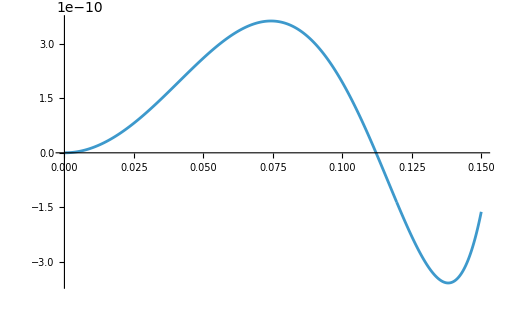

```mathematica
Plot[Vmub750[sigma^2/2]-Vmub750[0],{sigma,0,0.15}(*,ScalingFunctions->{Automatic,"Log"}*),PlotRange->{All,All}(*,Mesh->All*),PlotPoints->10000,MaxRecursion->10,WorkingPrecision->100,AccuracyGoal->100,PrecisionGoal->100]
```